## Computation of the exact expression of the conditional sweep probability

```mathematica
TildeNwt[xwt_]:=4/3*Pi*xwt^3
Delta1[xm_]:=4/3*Pi*xm^3
Delta2[xwt_,xm_]:=Pi/(12*y)*(xwt+xm+y)^2*(y^2+2*y*xm-3*xm^2+2*y*xwt+6*xwt*xm-3*xwt^2)
```

```mathematica
xwt[tau_]:=cwt*(tau+x/cwt)
xm[tau_]:=cm*tau
```

```mathematica
tau1=(x-y)/(cm-cwt)
tau2=(x+y)/(cm-cwt)
```

(x-y)/(cm-cwt)

(x+y)/(cm-cwt)

#### Integration over Delta2

```mathematica
Delta2[xwt[tau],xm[tau]]
```

(π (cm tau+cwt (tau+x/cwt)+y)^2 (-3 cm^2 tau^2+6 cm cwt tau (tau+x/cwt)-3 cwt^2 (tau+x/cwt)^2+2 cm tau y+2 cwt (tau+x/cwt) y+y^2))/(12 y)

```mathematica
FullSimplify[(π (cm tau+cwt (tau+x/cwt)+y)^2 (-3 cm^2 tau^2+6 cm cwt tau (tau+x/cwt)-3 cwt^2 (tau+x/cwt)^2+2 cm tau y+2 cwt (tau+x/cwt) y+y^2))/(12 y)]
```

(π ((cm+cwt) tau+x+y)^2 (-3 (-cm tau+cwt tau+x)^2+2 ((cm+cwt) tau+x) y+y^2))/(12 y)

```mathematica
Integrate[(π ((cm+cwt) tau+x+y)^2 (-3 (-cm tau+cwt tau+x)^2+2 ((cm+cwt) tau+x) y+y^2))/(12 y),{tau,tau1,tau2}]
```

(4 π y (30 cm^3 x^3+30 cm^2 (cm-cwt) x^2 y+15 cm (cm^2+cwt^2) x y^2+2 (cm-cwt) (cm+cwt)^2 y^3))/(45 (cm-cwt)^4)

#### Integration over Delta1

```mathematica
Delta1[xm[tau]]
```

4/3 cm^3 π tau^3

```mathematica
Integrate[4/3 cm^3 π tau^3,{tau,0,tau1}]
```

(cm^3 π (x-y)^4)/(3 (cm-cwt)^4)

#### Integration over \tilde{N}_wt

```mathematica
TildeNwt[xwt[tau]]
```

4/3 cwt^3 π (tau+x/cwt)^3

```mathematica
Integrate[4/3 cwt^3 π (tau+x/cwt)^3,{tau,0,tau1}]
```

(π (-x^4+(cm x-cwt y)^4/(cm-cwt)^4))/(3 cwt)

```mathematica
Integrate[4/3 cwt^3 π (tau+x/cwt)^3,{tau,tau1,tau2}]
```

(8 cm^3 π x^3 y)/(3 (cm-cwt)^4)+(8 cm cwt^2 π x y^3)/(3 (cm-cwt)^4)

#### The full solution is a sum over the results above

```mathematica
FullSimplify[((π (-x^4+(cm x-cwt y)^4/(cm-cwt)^4))/(3 cwt))-((cm^3 π (x-y)^4)/(3 (cm-cwt)^4))+((8 cm^3 π x^3 y)/(3 (cm-cwt)^4)+(8 cm cwt^2 π x y^3)/(3 (cm-cwt)^4))-((4 π y (30 cm^3 x^3+30 cm^2 (cm-cwt) x^2 y+15 cm (cm^2+cwt^2) x y^2+2 (cm-cwt) (cm+cwt)^2 y^3))/(45 (cm-cwt)^4))]
```

(π (15 (3 cm^2-3 cm cwt+cwt^2) x^4-210 cm^2 x^2 y^2-(23 cm^2+31 cm cwt+23 cwt^2) y^4))/(45 (cm-cwt)^3)

#### Plotting

```mathematica
Integ[x_,y_,cwt_,cm_]:=(π (15 (3 cm^2-3 cm cwt+cwt^2) x^4-210 cm^2 x^2 y^2-(23 cm^2+31 cm cwt+23 cwt^2) y^4))/(45 (cm-cwt)^3)
```

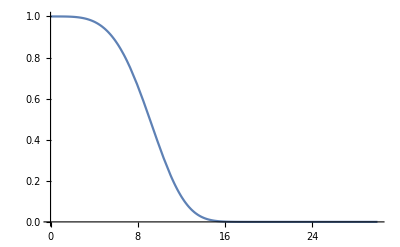

```mathematica
Plot[Exp[-10^(-5)*0.23*Integ[x,0,0.15,0.31]],{x,0,30}]
```

#### Checking coincidence with y=0 case.

```mathematica
FullSimplify[Integ[x,0,cwt,cm]]
```

((3 cm^2-3 cm cwt+cwt^2) π x^4)/(3 (cm-cwt)^3)